```mathematica
DateString[]
$Version
```

Wed 15 Mar 2023 15:23:45

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

## Lecture 04 by Chi-Ok Hwang, made by Dr. 전 경원

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

### 18 Geocomputation

18 Geocomputation

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"LosAngeles","California","UnitedStates"}]]
```

3914.03 km

Los Angeles

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],LinguisticAssistant]
```

3914.03 km

GeoDistance

GeoListPlot

GeoGraphics

GeoPosition

GeoNearest

Here

Picky exercises: 3, 5, 6, 10, 11, 12, +4

Tweet-a-Program:

```mathematica
GeoGraphics[Text[Style["Hello!",150]],GeoRange->"World"]
```

### 19 Dates and Times

19 Dates and Times

Now

DayRange

DayName

MoonPhase

Sunset

Sunrise

LocalTime

AirTemperatureData

DataListPlot

Picky exercises: 3, 7, +1,

### 20 Options

20 Options

Picky exercises: 4, 7, 9, 10, +3, +8



```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

& is shorthand for Function,and/@for Map

```mathematica
(#+3)&/@{1,2}
```

{4,5}

Prefix : An expression is called the prefix expression if the operator appears in the expression before the operands.Simply of the form (operator operand1 operand2).Example : *+AB - CD (Infix : (A + B)*(C - D))

Postfix : An expression is called the postfix expression if the operator appears in the expression after the operands.Simply of the form (operand1 operand2 operator).Example : AB + CD - *(Infix : (A + B*(C - D))

```mathematica
Abs[-3]
Abs@-3
```

3

3

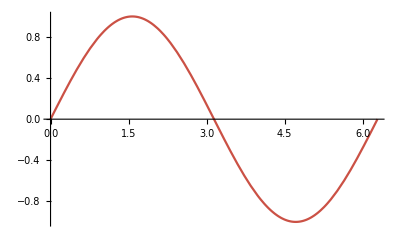

```mathematica
Plot[Sin[x],{x,0,2π},ColorFunctionScaling->False, ColorFunction->(ColorData["TemperatureMap"][Abs@#2]&)]
```

### 21 Graphs and Networks

21 Graphs and Networks

Graph

```mathematica
Table[RandomInteger[10]->RandomInteger[10],20]
```

{10→10,3→2,3→4,4→7,5→5,5→5,5→2,10→5,9→0,2→5,8→10,3→10,8→10,4→4,5→5,5→6,4→1,4→9,2→2,10→1}

```mathematica
Graph[Table[RandomInteger[10]->RandomInteger[10],20]]
```

-Graphics-

```mathematica
Table[Graph[Table[RandomInteger[10]->RandomInteger[10],20]],6]       (* Six randomly generated graphs *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

FindShortestPath

Flatten

UndirectedGraph

CommunityGraphPlot

Picky exercises: 9, +2, +3, +7

### 22 Machine Learning

22 Machine Learning

LanguageIdentify

ImageIdentify

Classify

Nearest

Blur

TextRecognize

FindClusters

NearestNeighborGraph

Dendrogram

FeatureSpacePlot

Picky exercises: 4, 8, 9, 12, 15, 16, +2, +3, +7

```mathematica
ImageRestyle[-Graphics-,Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

-Graphics-

### 23 More about Numbers

23 More about Numbers

```mathematica
N[Sqrt[200]]
```

14.1421

```mathematica
N[√200,10]
```

14.14213562

```mathematica
Prime[5]
```

11

Picky exercises: 10, 11, 14, +1

Tweet-a-Program:

```mathematica
StringDrop[ToString[N[π,10^6]],2];
StringPosition["abXYZaaabXYZaaaaXYZXYZ","XYZ"]
```

{{3,5},{10,12},{17,19},{20,22}}

```mathematica
First[StringPosition[StringDrop[ToString[N[π,10^6]],2],"770923"]]
```

{682619,682624}

### 24 More Forms of Visualization

24 More Forms of Visualization

Picky exercises: 2

Tweet-a-Program:

```mathematica
GeoElevationData[]
GeoDisk[]
ListPlot3D[GeoElevationData[%]]
```

172. m

GeoDisk[]

-Graphics3D-

```mathematica
GeoDisk[]
```

```mathematica
GeoDisk[]
Table[Style[Sin[x],ColorData["TemperatureMap"][Abs@Sin[x]]],{x,0,2π,0.1}]
```

GeoDisk[]

{0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471,0.891207,0.932039,0.963558,0.98545,0.997495,0.999574,0.991665,0.973848,0.9463,0.909297,0.863209,0.808496,0.745705,0.675463,0.598472,0.515501,0.42738,0.334988,0.239249,0.14112,0.0415807,-0.0583741,-0.157746,-0.255541,-0.350783,-0.44252,-0.529836,-0.611858,-0.687766,-0.756802,-0.818277,-0.871576,-0.916166,-0.951602,-0.97753,-0.993691,-0.999923,-0.996165,-0.982453,-0.958924,-0.925815,-0.883455,-0.832267,-0.772764,-0.70554,-0.631267,-0.550686,-0.464602,-0.373877,-0.279415,-0.182163,-0.0830894}

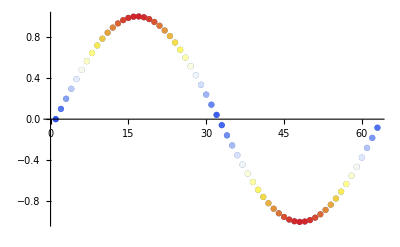

```mathematica
ListPlot@Table[Style[Sin[x],ColorData["TemperatureMap"][Abs@Sin[x]]],{x,0,2π,0.1}]
```